```mathematica
FullSimplify[Pi+2ArcCos[x]-4ArcCos[x/n]]
```

-2 ArcSin[x]+4 ArcSin[x/n]

```mathematica
D[-2 ArcSin[x]+4 ArcSin[x/n],x]
```

-2/(√(1-x^2))+4/(n √(1-x^2/n^2))

```mathematica
Solve[-2/(√(1-x^2))+4/(n √(1-x^2/n^2))==0,x]
```

{{x→-(√(4-n^2))/(√3)},{x→(√(4-n^2))/(√3)}}

```mathematica
Solve[D[-2 ArcSin[x]+4 ArcSin[x/n],x]==0,x]
```

{{x→-(√(4-n^2))/(√3)},{x→(√(4-n^2))/(√3)}}

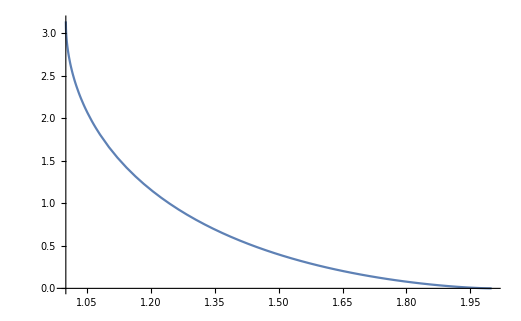

```mathematica
Plot[-2 ArcSin[(√(4-n^2))/(√3)]+4 ArcSin[(√(4-n^2))/(√3 n)],{n,1,2}]
```

```mathematica
With[{n=#},-2 ArcSin[(√(4-n^2))/(√3)]+4 ArcSin[(√(4-n^2))/(√3 n)]]&/@{1.3,1.33,1.34,1.4}
```

{0.822611,0.742051,0.716824,0.580294}

```mathematica
%*180/Pi
```

{47.1321,42.5164,41.071,33.2484}